```mathematica
(*Уравнение прямой на плоскости*)
canonicalEq = y==k*x+m;
(*Точки*)
a = {y->ya,x->xa};
b = {y->yb,x->xb};
c = {y->yc,x->xc};
(*Вывод уравнения прямой, проходящей через a,b*)
eq1=canonicalEq/.a;
eq2=canonicalEq/.b;
resLine=Solve[{eq1,eq2},{k,m}]//First//Simplify;
lineEq = canonicalEq/.resLine
```

y==(x (ya-yb))/(xa-xb)+(-xb ya+xa yb)/(xa-xb)

```mathematica
(*Направляющий вектор этой линии*)
lineVec={1,k}/.resLine
```

{1,(ya-yb)/(xa-xb)}

```mathematica
rotMatr = {{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}};
(*Направляющий вектор перпендикуляра к этой линии*)

lineOrthVec = rotMatr.lineVec/.θ->Pi/2
lineOrthVec =lineOrthVec/lineOrthVec[[1]]
```

{-(ya-yb)/(xa-xb),1}

{1,-(xa-xb)/(ya-yb)}

```mathematica
(*Уравнение прямой, проходящей через c и перпендикулярной первой*)
eq3=canonicalEq /.c;
resLineOrth={k->lineOrthVec[[2]],Solve[eq3/.k->lineOrthVec[[2]],m][[1,1]]};
lineOrthEq=canonicalEq/.resLineOrth
```

y==-(x (xa-xb))/(ya-yb)+(xa xc-xb xc+ya yc-yb yc)/(ya-yb)

```mathematica
(*Координаты точки пересечения линии и перпендикуляра*)
resIntersect = Simplify[Solve[{lineEq,lineOrthEq},{x,y}], Assumptions->{Element[x,Reals] ,Element[y,Reals]}]//First
```

{x→(xa^2 xc-2 xa xb xc+xb^2 xc+xb (ya-yb) (ya-yc)-xa (ya-yb) (yb-yc))/(xa^2-2 xa xb+xb^2+(ya-yb)^2),y→(xb^2 ya+xa^2 yb+xb xc (-ya+yb)-xa (xc (-ya+yb)+xb (ya+yb))+(ya-yb)^2 yc)/(xa^2-2 xa xb+xb^2+(ya-yb)^2)}

```mathematica
(*Расстояние от точки с до линии*)
dist=Sqrt[(x-xc)^2+(y-yc)^2]/.resIntersect//Simplify
dist=Simplify[%, Assumptions->{Element[x,Reals] ,Element[y,Reals]}]
```

√((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2/(xa^2-2 xa xb+xb^2+(ya-yb)^2))

√((xb ya-xc ya-xa yb+xc yb+xa yc-xb yc)^2/(xa^2-2 xa xb+xb^2+(ya-yb)^2))

{103/25,-29/25}

y==13/3-(4 x)/3

y==-17/4+(3 x)/4

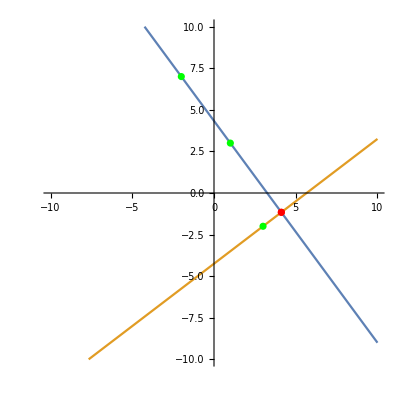

```mathematica
(*А чего бы все это не нарисовать?*)
aTest={xa->1,ya->3};
bTest={xb->-2,yb->7};
cTest={xc->3,yc->-2};
aPointTest={xa,ya}/.aTest;
bPointTest={xb,yb}/.bTest;
cPointTest={xc,yc}/.cTest;
intersectPointTest={x,y}/.resIntersect/.aTest/.bTest/.cTest
lineEqTest=lineEq/.aTest/.bTest/.cTest
lineOrthEqTest=lineOrthEq/.aTest/.bTest/.cTest
plt1=Plot[{13/3-(4 x)/3,-17/4+(3 x)/4},{x,-10,10},PlotRange->{{-10,10},{-10,10}},AspectRatio->1];
plt2=ListPlot[{aPointTest,bPointTest,cPointTest},PlotStyle->Green];

plt3=ListPlot[{intersectPointTest},PlotStyle->Red];
Show[{plt1,plt2,plt3}]
```